```mathematica
eq1=Cos[θ/2]==d/((r-w/2)*(1/Cos[θ/2]-1));
eq2=Tan[θ/2]==ell/r;
First@Solve[eq1,r]
First@Solve[eq2,ell]
FullSimplify@First@Solve[eq2,ell]/.First@Solve[eq1,r]
(*First@Solve[(r-w/2)/(r-w/2+(d+w/2)/Cos[θ/2])==Cos[θ/2],r]*)
```

{r→-1/4 (-2 d-w+w Cos[θ/2]) Csc[θ/4]^2}

{ell→r Tan[θ/2]}

{ell→-1/4 (-2 d-w+w Cos[θ/2]) Csc[θ/4]^2 Tan[θ/2]}

0.332151

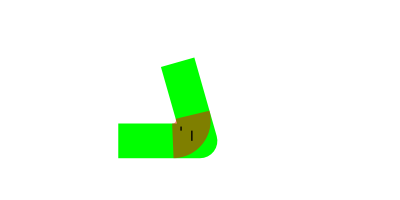

```mathematica
θ=π/1.7;
w=0.25;
d=0.05;
r=-1/4 (-2 d-w+w Cos[θ/2]) Csc[θ/4]^2;
l=r*Tan[θ/2]
Graphics[{JoinForm["Round"],CapForm["Round"],{Thickness[w/4],Green,Line[{{-1,0},{0,0},{Cos@θ,Sin@θ}}]},
{Thickness[w/4],Opacity[0.5],Red,Circle[{-l,r},r,{3π/2,3π/2+θ}]},Black,Line[{{-Sin[θ/2]*w/2,0},{-Sin[θ/2]*w/2,w/2}}],Line[{{-l+(r-w/2)*Sin[θ/2],w/2+d},{-l+(r-w/2)*Sin[θ/2],w/2}}]},PlotRange->{{-2,2},{-0.5,1.5}}]
Manipulate[r=-1/4 (-2 d-w+w Cos[θ/2]) Csc[θ/4]^2;l=r*Tan[θ/2];Graphics[{JoinForm["Round"],CapForm["Round"],
{Thickness[w/4],Green,Line[{{-2,0},{0,0},{2*Cos@θ,2*Sin@θ}}]},
{Thickness[w/4],Opacity[0.5],Red,Circle[{-l,r},r,{3π/2,3π/2+θ}]},Black,Line[{{-l+(r-w/2)*Sin[θ/2],w/2+d},{-l+(r-w/2)*Sin[θ/2],w/2}}]},PlotRange->{{-2,2},{-0.5,1.5}}],{{θ,π/3,"Angle"},π/20,π},{{w,0.25,"Trace thickness"},0.01,0.75},{{d,0.05,"Path deviation"},0.0,0.6}]
```